# Lab #12

## Craig Fox

Clear initial definitions

```mathematica
Remove["Global`*"]
```

Initial data points

```mathematica
lengthsInInches={70,59,47,33,26,19,8};
timesForTenSeconds={26.75,24.86,21.81,18.29,16.13,13.78,8.87};
```

Converting data to proper units

```mathematica
lengths=lengthsInInches*.0254
times=timesForTenSeconds/10
```

{1.778,1.4986,1.1938,0.8382,0.6604,0.4826,0.2032}

{2.675,2.486,2.181,1.829,1.613,1.378,0.887}

Calculate gravity

```mathematica
gravity=4*Pi^2*lengths/(times^2)
```

{9.80943,9.57289,9.90786,9.89191,10.0207,10.0334,10.1961}

FInd mean

```mathematica
g=Mean[gravity]
```

9.91891

Find standard deviation

```mathematica
σ=StandardDeviation[gravity]
```

0.197018

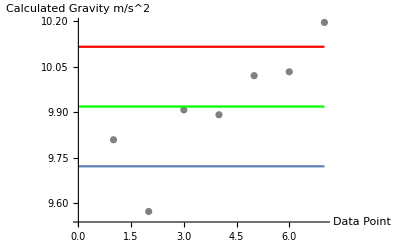

```mathematica
Show[{ListPlot[gravity,PlotStyle->Gray],Plot[g,{x,0,7},PlotStyle->Green],Plot[g+σ,{x,0,7},PlotStyle->Red],Plot[g-σ,{x,0,7}]},{PlotStyle->Blue,AxesLabel->{Data Point,Calculated Gravity "m/s^2"}}]
```